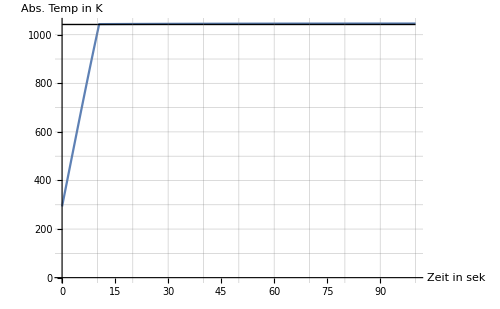

```mathematica
data = Import[FileNameJoin[{NotebookDirectory[],"TempGraph.txt"}], "Data"];
ListLinePlot[data, GridLines->{Table[10*i, {i,0,Ceiling[Max[data[[All,1]]]/10]}],Table[100*i, {i,0,Ceiling[Max[data[[All,2]]]/100]}]},PlotRange->All, AxesLabel->{"Zeit in sek","Abs. Temp in K"},ImageSize->500, Epilog->{Line[{{0, 1042.15},{Ceiling[Max[data[[All,1]]]],1042.15}}]}]
```